```mathematica
phi1[x_]:=Sqrt[2]Sin[Pi x]
```

```mathematica
phi2[x_]:=Sqrt[2]Sin[2 Pi x]
```

```mathematica
phi:=1/Sqrt[2] Det[{{phi1[x],phi2[x]},{phi1[y],phi2[y]}}]
```

```mathematica
ContourPlot[phi,{x,-1,1},{y,-1,1},PlotLegends->Automatic,ColorFunction->GrayLevel]
```

-Graphics-

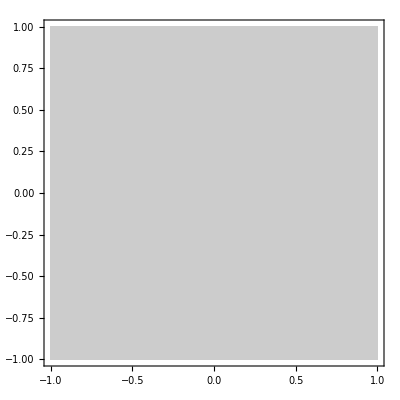

```mathematica
ContourPlot[1/Sqrt[2] Det[{{phi1[x],phi2[x]},{phi1[x],phi2[x]}}],{x,-1,1},{y,-1,1},PlotLegends->Automatic,ColorFunction->GrayLevel]
```

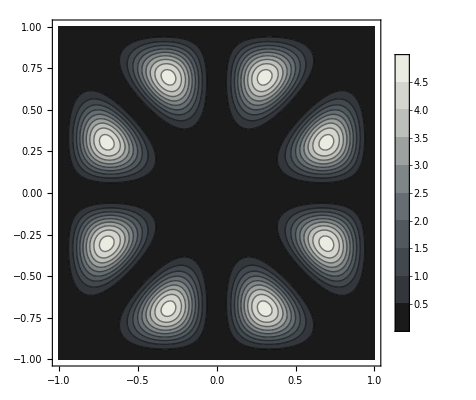

```mathematica
ContourPlot[phi^2,{x,-1,1},{y,-1,1},PlotLegends->Automatic,ColorFunction->"GrayTones"]
```